High Energy Electromagnetic Conversion Processes in Intense Magnetic Fields

Thomas Erber, Rev Mod Physics 38 4 1966
Notebook: Óscar Amaro, October 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## Figure 3: Graph of the bremsstrahlung function

2^(2/3) z^(1/3) Gamma[2/3] HypergeometricPFQ[{-1/3},{-2/3,2/3},z^2/4]+(π z (-320+(81 2^(1/3) z^(8/3) HypergeometricPFQ[{4/3},{7/3,8/3},z^2/4])/Gamma[-1/3]))/(320 √3)

2.14953 z^(1/3)-1.8138 z

Series::ztest1: Unable to decide whether numeric quantity -π/(√3)-1/3 (-1)^(1/3) Gamma[-2/3] Gamma[2/3]+(2 (-1)^(2/3) π^2)/(3 Gamma[-1/3] Gamma[4/3]) is equal to zero. Assuming it is.

(0.957393 ⅇ^(-1. z))/(√z)+1.25331 ⅇ^(-1. z) √z

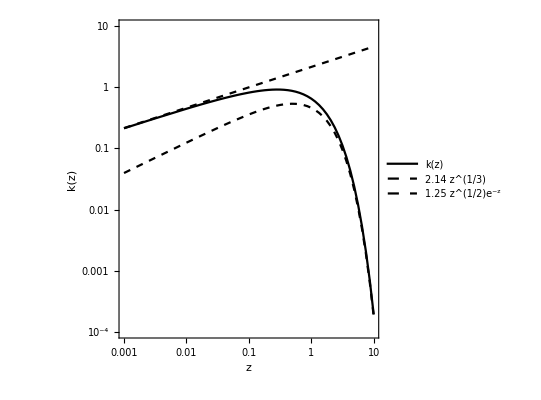

TABLE I

z | k(z)

0.001 | 0.213139
0.01 | 0.444973
0.02 | 0.547239
0.03 | 0.613607
0.04 | 0.662796
0.05 | 0.701572
0.06 | 0.733248
0.07 | 0.759722
0.08 | 0.782199
0.09 | 0.801493
0.1 | 0.818186
0.2 | 0.903386
0.3 | 0.917705
0.4 | 0.901937
0.5 | 0.870819
0.6 | 0.831475
0.7 | 0.787875
0.8 | 0.742413
0.9 | 0.696603
1 | 0.651423
2 | 0.301636
3 | 0.128566
4 | 0.0528274
5 | 0.0212481
6 | 0.00842608
7 | 0.00330761
8 | 0.00128845
9 | 0.000498893
10 | 0.000192238

```mathematica
Clear[k,z,x]
k=z Integrate[BesselK[5/3,x],{x,z,∞}]//Normal//Simplify

(* z->0, see also A27 *)
Series[k,{z,0,2}]//Normal//N

(* z-> ∞*)
Asymptotic[Asymptotic[k,z->∞,SeriesTermGoal->2]//Simplify//N//Simplify//Chop,z->∞,SeriesTermGoal->1]

(*k[z_]:=NIntegrate[BesselK[5/3,x],{x,z,∞}]*)
LogLogPlot[{k,2.1495282415344787z^(1/3),1.2533141373155 Sqrt[z]Exp[-z]},{z,10^-3,10^1},PlotRange->{{10^-3,10^1},{10^-4,10^1}},AspectRatio->1,Frame->True,FrameLabel->{"z","k(z)"},PlotPoints->2,PlotStyle->{Black,Directive[Black,Dashed],Directive[Black,Dashed]},PlotLegends->{"k(z)","2.14 z^(1/3)","1.25 z^(1/2)e^-z"}]

Print["TABLE I"]
Print["z | k(z)"]
zlst=Flatten[{0.001,Table[i 0.01,{i,1,9}],Table[i 0.1,{i,1,9}],Table[i ,{i,1,10}]}];
klst=Table[k/.{z->zlst[[i]]}//N,{i,1,Length[zlst]}];
TableForm[Transpose[{zlst,klst}]]
```

```mathematica
Clear[k,z,x,f,y]
k[z_?NumericQ]:=k[z]=z NIntegrate[BesselK[5/3,x],{x,z,∞}]//Quiet
(* eq 2.23b *)
f[y_]:=3/2(y^2 k[y]+3NIntegrate[z k[z],{z,y,∞}])/NIntegrate[k[z],{z,y,∞}]//Quiet
(* "table" 2.23c *)
f[1]
f[2]
f[3]
```

10.9245

19.2364

30.5554

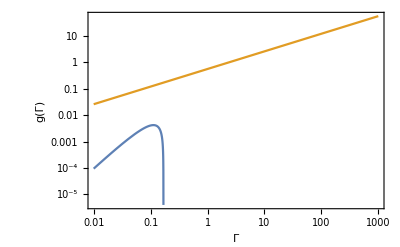

```mathematica
(* Figure 4 *)
LogLogPlot[{Γ^2(1-5.953 Γ),0.5563 Γ^(2/3)},{Γ,10^-2,10^3},Frame->True,FrameLabel->{"Γ","g(Γ)"}]
```

Table II: h(Z; A,ρ,α) is defined in 2.31b

```mathematica
Clear[ρ,α,Z,A,h]
h=6(ρ/A)(α Z)^2(Log[183/Z^(1/3)]+0.083-1.2(α Z)^2(1-0.86(α Z)^2));
α=1/137;
Zlst={"Z",4,7,8,13,29,82,92};
Alst={"A",9,14,16,27,63,204,238};
ρlst={"ρ",1.84,1.25 10^-3,1.7,2.7,8.89,11,18.7};
hlst={"h",Table[h/.{Z->Zlst[[i]],ρ->ρlst[[i]],A->Alst[[i]]},{i,2,Length[Zlst]}]}//Flatten;
Print["Beryllium | Air | High explosive | Aluminium | Copper | Lead | Uranium"]
TableForm[{Zlst,Alst,ρlst,hlst}]
```

Beryllium | Air | High explosive | Aluminium | Copper | Lead | Uranium

Z | 4 | 7 | 8 | 13 | 29 | 82 | 92
A | 9 | 14 | 16 | 27 | 63 | 204 | 238
ρ | 1.84 | 0.00125 | 1.7 | 2.7 | 8.89 | 11 | 18.7
h | 0.00505005 | 6.49044×10^-6 | 0.00998916 | 0.0239158 | 0.15624 | 0.408694 | 0.734287

## Figure 9

```mathematica
Clear[T,χ,u,w,tab]
(* in this formulation, the double numerical integral can lead to some integration imprecision *)
T[χ_]:=4/(3π^2 χ^2)NIntegrate[NIntegrate[(2Cosh[w]^2Cosh[u]^5-Sinh[u]^2Cosh[u]^3)BesselK[1/3,2/(3χ)Cosh[w]^2Cosh[u]^3]^2 + (2Cosh[w]^2-1)Cosh[u]^5 BesselK[2/3,2/(3χ)Cosh[w]^2Cosh[u]^3]^2,{u,0,∞}]//Quiet,{w,0,∞}]//Quiet
tab=ParallelTable[{10^x,1/2 T[10^x]},{x,-1,4,0.5}];
```

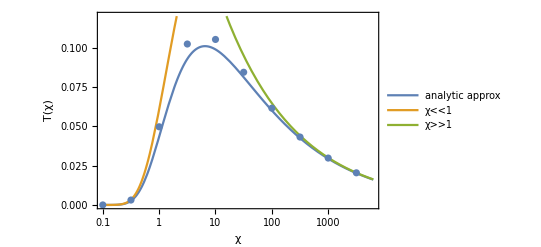

```mathematica
(* maximum value of T would be different from fig9 without the factor of 1/2 *)
Show[{LogLinearPlot[{1/2 0.16/χ BesselK[1/3,2/(3χ)]^2,1/2 0.46Exp[-4/(3χ)],1/2 0.6/χ^(1/3)},{χ,10^-1,10^3.8},PlotRange->{0,0.12},Frame->True,FrameLabel->{"χ","T(χ)"},PlotLegends->{"analytic approx","χ<<1","χ>>1"}],ListLogLinearPlot[tab,PlotLegends->"3.2b"]}]
```

Table VI.

```mathematica
Clear[χlst,Tlst]
χlst={0.2,0.3,0.4,0.7,1.2,3,5,6,7,9,15,30};
Tlst=ParallelTable[(1/2 0.16/χ BesselK[1/3,2/(3χ)]^2/.{χ->χlst[[i]]}),{i,1,Length[χlst]}];
Print["χ | T(χ)"]
TableForm[Transpose[{χlst,Tlst}]]
```

χ | T(χ)

0.2 | 0.000231226
0.3 | 0.00210049
0.4 | 0.0062894
0.7 | 0.025274
1.2 | 0.0531372
3 | 0.0915078
5 | 0.0999294
6 | 0.100821
7 | 0.100851
9 | 0.0996915
15 | 0.0939284
30 | 0.0821556

## 4. TRIDENT CASCADES

```mathematica
Clear[χ,W]
(* eq 4.3b *)
W[χ_]:=χ BesselK[0,χ]BesselK[1,χ]-χ^2/2 (BesselK[1,χ]^2-BesselK[0,χ]^2)

(* χ<<1 *)
Series[W[χ],{χ,0,1}]//Normal//N//Chop//Expand
(* χ>>1 *)
Asymptotic[W[χ],χ->∞,SeriesTermGoal->1]
```

-0.384068-1. Log[χ]

1/4 ⅇ^(-2 χ) π

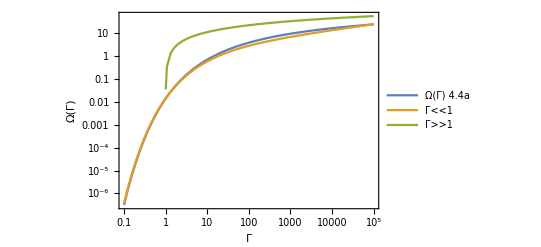

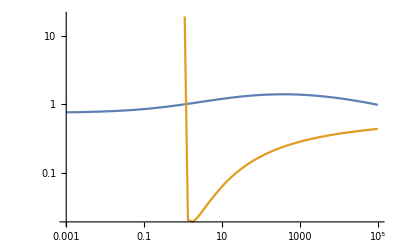

```mathematica
Clear[χ,W,Ω,Γ,u]
(* eq 4.3b *)
W[χ_]:=χ BesselK[0,χ]BesselK[1,χ]-χ^2/2 (BesselK[1,χ]^2-BesselK[0,χ]^2)
Ω[Γ_]:=NIntegrate[u^-2 W[u/Γ]BesselK[1/3,4/(3u)]^2,{u,0,∞}]
LogLogPlot[{Ω[Γ],π^(5/2)/16(3Γ)^(1/4)Exp[-8(3Γ)^(-1/2)],π^2/2 Log[Γ]},{Γ,10^-1,10^5},PlotPoints->2,Frame->True,FrameLabel->{"Γ","Ω(Γ)"},PlotLegends->{"Ω(Γ) 4.4a","Γ<<1","Γ>>1"}]
(* ratio *)
LogLogPlot[{Ω[Γ]/(π^(5/2)/16(3Γ)^(1/4)Exp[-8(3Γ)^(-1/2)]),Ω[Γ]/(0.5 π^2 Log[Γ])},{Γ,10^-3,10^5},PlotPoints->2]
```

## 5: Cherenkov radiation and photon splitting

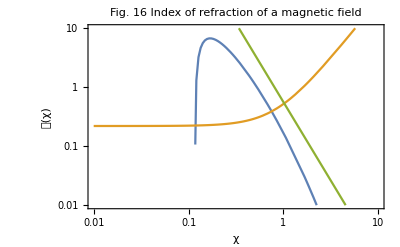

{1.45076,{χ→0.3}}

{χ→9.38354}

```mathematica
Clear[χ,χtil,dI,ν,𝒥,dv,dIp13,dIm13]
(*
(* differentiation with respect to index will not work with: *)
dv=1;dI[ν_?NumericQ,x_?NumericQ]:=dI[ν,x]=(BesselI[ν+dv,x]-BesselI[ν,x])/dv;*)

(* instead, follow the series formulation as in https://functions.wolfram.com/Bessel-TypeFunctions/BesselI/20/01/01/0001/ *)
(*BesselI[ν,z] Log[z/2]-Sum[(PolyGamma[1+k+ν]/(k! Gamma[1+k+ν])) (z/2)^(2 k+ν),{k,0,Infinity}]//.{ν->-1/3}//Simplify*)
dI[ν_,z_]:=BesselI[ν,z] Log[z/2]-Sum[(PolyGamma[1+k+ν]/(k! Gamma[1+k+ν])) (z/2)^(2 k+ν),{k,0,Infinity}]
dIp13[z_]:=BesselI[1/3,z] (Log[z/2]-PolyGamma[0,4/3])-1/2^(1/3)z^(1/3) Gamma[4/3] Derivative[{1},{0,0},0][HypergeometricPFQRegularized][{4/3},{4/3,4/3},z^2/4]
dIm13[z_]:=BesselI[-1/3,z] (Log[z/2]-PolyGamma[0,2/3])-1/z^(1/3)2^(1/3) Gamma[2/3] Derivative[{1},{0,0},0][HypergeometricPFQRegularized][{2/3},{2/3,2/3},z^2/4]

𝒥[χtil_]:=-0.027 π^2(3/2 χtil)^-2(BesselK[1/3,χtil](BesselI[1/3,χtil]+BesselI[-1/3,χtil])+2(BesselI[-1/3,χtil]dIp13[χtil]+BesselI[1/3,χtil]dIm13[χtil]))

LogLogPlot[ {𝒥[χtil]/.{χtil->2/3 χ},0.22+0.3 χ^2,0.56 χ^(-2 4/3)},{χ,10^-2,10^1},PlotPoints->3,PlotRange->{{10^-2,10^1},{0.01,10}},Frame->True,FrameLabel->{"χ","𝒥(χ)"},PlotLabel->"Fig. 16 Index of refraction of a magnetic field"]

FindMaximum[𝒥[χ],{χ,.3}]//Quiet
FindRoot[𝒥[χ],{χ,7}]//Quiet
```

Table IX

```mathematica
Clear[χlst,𝒥lst]
χlst={0.17,0.22,0.4,1,2.22,3.33,6.66,9.52};
𝒥lst=ParallelTable[(𝒥[χ]/.{χ->χlst[[i]]}//N),{i,1,Length[χlst]}];
Print["χ | 𝒥(χ)"]
TableForm[Transpose[{χlst,𝒥lst}]]
```

χ | 𝒥(χ)

0.17 | 4.50699
0.22 | 2.83711
0.4 | 0.713651
1 | 0.0442083
2.22 | 0.002045
3.33 | 0.000379695
6.66 | 0.000022448
9.52 | 5.3357×10^-6

## Appendix 1:

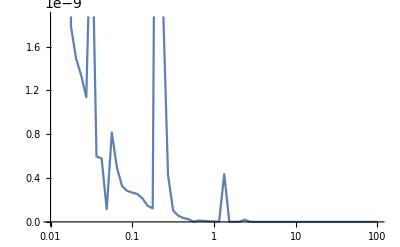

```mathematica
(* prove identity 2.8e: difference is near machine precision *)
Clear[x,ζ,int1,int2]
int1[ζ_]:=π/(2√3 ζ)NIntegrate[BesselK[5/3,x],{x,2ζ,∞}]//Normal//Simplify
int2[ζ_]:=NIntegrate[Cosh[x]^5 BesselK[2/3,ζ Cosh[x]^3]^2+Cosh[x]^3 Sinh[x]^2 BesselK[1/3,ζ Cosh[x]^3]^2,{x,0,∞}]
LogLinearPlot[{Abs[int1[ζ]-int2[ζ]]},{ζ,10^-2,10^2},PlotPoints->2]
```

## Appendix 2:

{0.918012,{z→0.285812}}

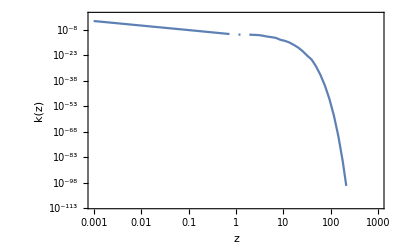

2.5602×10^-8

0

```mathematica
Clear[k,z,x,f,y,dz,A23]
(* A22 *)
k[z_?NumericQ]:=k[z]=z NIntegrate[BesselK[5/3,x],{x,z,∞}]//Re//Quiet
s=FindMaximum[k[z],{z,2}]
(*k[s[[2,1,2]]]*)

(* A23: near machine precision *)
dz=10^-5;
A23[z_]:=Abs[(k[z+dz]-k[z-dz])/(2dz)-(1/z k[z]-(4/3 BesselK[2/3,z]+z BesselK[1/3,z]))]
LogLogPlot[A23[z],{z,10^-3,10^3},PlotPoints->2,Frame->True,FrameLabel->{"z","k(z)"}]

(* derivative should be ~0 *)
dk=D[z Integrate[BesselK[5/3,x],{x,z,∞}],z]//Normal//Simplify;
dk/.{z->s[[2,1,2]]}

(* Bessel function transformation (before A24) *)
Refine[BesselK[5/3,x]-(-(BesselK[1/3,x]+2D[BesselK[2/3,x],x])),{x>0}]//FullSimplify
```

```mathematica
(* A25: not implemented *)
Clear[Kν,x,nmax,nmin]
nmin=0;
Kν[x_,ν_,nmax_]:=(π/2)/Sin[ν π]((x/2)^-ν Sum[(x/2)^(2n)/(n! Gamma[n-ν+1]),{n,nmin,nmax}]-(x/2)^ν Sum[(x/2)^(2n)/(n! Gamma[n+ν+1]),{n,nmin,nmax}])
Kν[10,2,10]
BesselK[10,2]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

BesselK[10,2]

```mathematica
LogLogPlot[{Kν[x,2,5]},{x,10^-1,10^2},PlotPoints->2]
```

```mathematica
(* to obtain A26 expansion *)
Clear[khat,x,z,series]
khat=Integrate[BesselK[1/3,x],{x,0,z}]//Normal//Simplify;
series=Series[khat,{z,0,8}]//N//Chop
(* z^(2/3) series *)
{series[[3,1]],series[[3,7]],series[[3,13]],series[[3,19]]}/2.531438288439613
(* z^(4/3) series *)
{series[[3,3]],series[[3,9]],series[[3,15]],series[[3,21]]}/-1.2091096358631443
```

2.53144 z^(2/3)-1.20911 z^(4/3)+0.237322 z^(8/3)-0.0906832 z^(10/3)+0.010171 z^(14/3)-0.00303627 z^(16/3)+0.00022249 z^(20/3)-0.0000552049 z^(22/3)+O[z]^(26/3)

{1.,0.09375,0.00401786,0.0000878906}

{1.,0.075,0.00251116,0.0000456575}

```mathematica
(* threshold energy 5.6a *)
((2π)/(1/137 0.25))^(1/2)
```

58.6787

## Appendix 4: Evaluation of the auxiliary function Ξ(Γ)